```mathematica
<< peeters`;
peeters`setGitDir["../project/figures/ece1505-convex-optimization"]
```

/Users/pjoot/project/figures/ece1505-convex-optimization

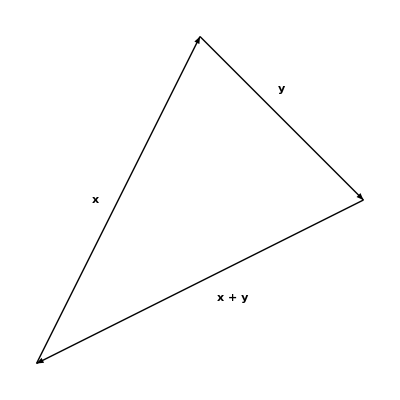

```mathematica
ClearAll[o, x,y, bold, p1]
o = {0,0};
x = {1,2}/2;
y = {0.5,-0.5};
bold  := (Style[#, Bold,Large])&;

p1 =Graphics[{Arrowheads[0.07],Arrow[{o,x}],Arrow[{x,x + y}],Arrow[{x + y,o}],
Text[ bold["x"], x/2 - {0.07,0}],
Text[ bold["y"], x + (y)/2 + {0,0.09}],
Text[ bold["x + y"],( x + y)/2 - {-0.1,0.05}]
}]
```

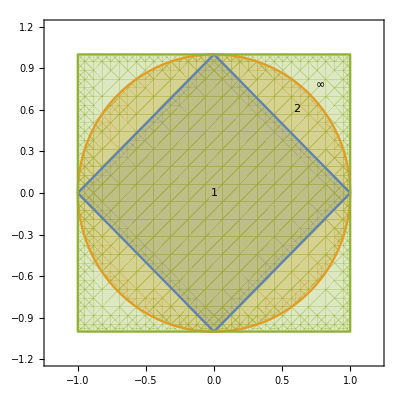

```mathematica
ClearAll[pnorm,x,y,p2, large]
large := Style[#, Medium]&;

p2 =Show[Block[{r = 1.2},
RegionPlot[ (Norm[{x,y}, #] < 1 &/@ {1,2,Infinity})//Evaluate, {x, -r,r},{y,-r,r}(*, 
PlotLegends->Placed["Expressions", {Top, Right}]*)
]
],
Graphics[
{
Text[large[1],{0,0}],
Text[Infinity // large,{1.1,1.1}/Sqrt[2]],
Text[2// large,{1,1}(1/Sqrt[2]+1/2)/2]
}
]
]
```

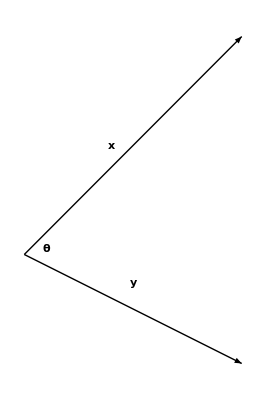

```mathematica
ClearAll[x,y, p3]
x = {1,1}/2;
y = {0.5,-0.25};

p3 =Graphics[{Arrowheads[0.07],Arrow[{o,x}],Arrow[{o,y}],
Text[ bold["x"], x/2 - {0.05,0}],
Text[ bold["y"], (y)/2 + {0,0.06}],
Text[ bold["θ"],( x + y)/20 ]
}]
```

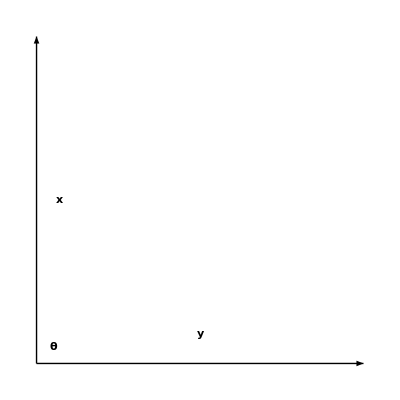

```mathematica
ClearAll[x,y, p4]
x = {0,1};
y = {1,0};

p4 =Graphics[{Arrowheads[0.07],Arrow[{o,x}],Arrow[{o,y}],
Text[ bold["x"], x/2 + {0.07,0}],
Text[ bold["y"], (y)/2 + {0,0.09}],
Text[ bold["θ"],( x + y)/20 ]
}]
```

```mathematica
peeters`exportForLatex[ "L2XPlusYFig1", p1]
peeters`exportForLatex[ "L2NormsFig2", p2]
peeters`exportForLatex[ "L2XYThetaFig3", p3]
peeters`exportForLatex[ "L2XYRightAngleFig4", p4]
```

{L2XPlusYFig1.eps,L2XPlusYFig1pn.png}

{L2NormsFig2.eps,L2NormsFig2pn.png}

{L2XYThetaFig3.eps,L2XYThetaFig3pn.png}

{L2XYRightAngleFig4.eps,L2XYRightAngleFig4pn.png}

```mathematica
pnorm[0.5]
```

Norm::ptype: The second argument of Norm, 0.5, should be a symbol, Infinity, or an integer or real number not less than 1 for vector p-norms; or 1, 2, Infinity, or "Frobenius" for matrix norms.

-Graphics-

```mathematica
ClearAll[norm,pnorm]
norm[{x_,y_}, p_] := (Abs[x]^p + Abs[y]^p)^(1/p) ;
pnorm[p_] := RegionPlot[ norm[{x,y}, p] < 1, {x, -1.2,1.2},{y,-1.2,1.2}];


Manipulate[
pnorm[p],
{{p,2},0.1, 25}]
(*Show[pnorm[2],pnorm[1],pnorm[Infinity]]*)
```

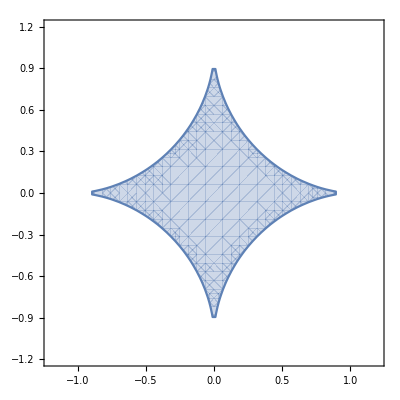

{l4PNormPLessThan1Fig7a.eps,l4PNormPLessThan1Fig7apn.png}

```mathematica
p7 = pnorm[0.6]
peeters`exportForLatex[ "l4PNormPLessThan1Fig7a", p7]
```